字符串与文本

Wolfram 语言可以让你计算的另一个对象是文本。你可以把文本作为字符串进行输入，用引号(")表示。

输入字符串：

```mathematica
"This is a string."
```

This is a string.

就像你输入数字一样，字符串也是原样返回，只是在显示字符串的时候引号不见了。有许多函数适用于字符串，比如 StringLength，它将给出一个字符串的长度。

StringLength 用于计算字符串中的字符数：

```mathematica
StringLength["hello"]
```

5

StringReverse 用于反转字符串中的字符：

```mathematica
StringReverse["hello"]
```

olleh

ToUpperCase 用于将字符串中的所有字符变成大写形式：

```mathematica
ToUpperCase["I'm coding in the Wolfram Language!"]
```

I'M CODING IN THE WOLFRAM LANGUAGE!

StringTake 用于从一个字符串的开头取出指定数量的字符：

```mathematica
StringTake["this is about strings",10]
```

this is ab

如果你取出 10 个字符，你会得到一个长度为 10 的字符串：

```mathematica
StringLength[StringTake["this is about strings",10]]
```

10

StringJoin 用于连接字符串(如果你想将单词分隔开，别忘了添加空格)：

```mathematica
StringJoin["Hello"," ", "there!", " How are you?"]
```

Hello there! How are you?

你可以创建字符串列表，然后对它们应用函数：

一个字符串列表：

```mathematica
{"apple","banana","strawberry"}
```

{apple,banana,strawberry}

从每个字符串中获取前两个字符：

```mathematica
StringTake[{"apple","banana","strawberry"},2]
```

{ap,ba,st}

StringJoin 可以将一个列表中的字符串连接在一起：

```mathematica
StringJoin[{"apple","banana","strawberry"}]
```

applebananastrawberry

有时，把字符串变成其组成字符的列表是很有用的。每个字符实际上都是一个字符串，长度为 1。

Characters 用于将一个字符串分解成一个字符列表：

```mathematica
Characters["a string is made of characters"]
```

{a, ,s,t,r,i,n,g, ,i,s, ,m,a,d,e, ,o,f, ,c,h,a,r,a,c,t,e,r,s}

一旦你把一个字符串分解成了一个字符列表，你就可以对它使用所有常用的列表函数。

排列字符串中的字符顺序：

```mathematica
Sort[Characters["a string of characters"]]
```

{ , , ,a,a,a,c,c,e,f,g,h,i,n,o,r,r,r,s,s,t,t}

列表开头的不可见元素是空格字符。如果你想以你输入的形式看到字符串，包含 "..." 的完整形式，请使用 InputForm。

InputForm 用于显示你输入的字符串，包括引号：

```mathematica
InputForm[Sort[Characters["a string of characters"]]]
```

{" ", " ", " ", "a", "a", "a", "c", "c", "e", "f", "g", "h", "i", "n", "o", "r", 
 "r", "r", "s", "s", "t", "t"}

像 StringJoin 和 Characters 这样的函数适用于任何类型的字符串；它们是否是有意义的文本并不重要。还有一些函数，比如 TextWords，则专门针对有意义的文本，比如用英语写的。

TextWords 将给出一串文本中的单词列表：

```mathematica
TextWords["This is a sentence. Sentences are made of words."]
```

{This,is,a,sentence,Sentences,are,made,of,words}

这将给出了每个单词的长度：

```mathematica
StringLength[TextWords["This is a sentence. Sentences are made of words."]]
```

{4,2,1,8,9,3,4,2,5}

TextSentences 用于将一个文本字符串分解为一个句子列表：

```mathematica
TextSentences["This is a sentence. Sentences are made of words."]
```

{This is a sentence.,Sentences are made of words.}

有很多方法可以将文本输入 Wolfram 语言。一个例子是 WikipediaData 函数，它可以获得英文维基百科文章的当前文本。

获取维基百科中关于“计算机”的文章的前 100 个字符：

```mathematica
StringTake[WikipediaData["computers"],100]
```

A computer is a general-purpose device that can be programmed to carry out a set of arithmetic or lo

要了解一段文本中的内容，一个方便的方法是创建一个词云。函数 WordCloud 可以完成这样的功能。

为维基百科关于“计算机”的文章创建一个词云：

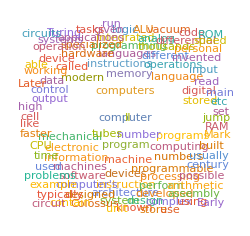

```mathematica
WordCloud[WikipediaData["computers"]]
```

毫不奇怪，“computer”和“computers”是该文章中最常见的词汇。

Wolfram 语言中有很多关于英语和其他语言中出现的单词的内置知识。WordList 将给出单词的列表。

获取常见的英语单词列表中的前 20 个单词：

```mathematica
Take[WordList[ ],20]
```

{a,aah,aardvark,aback,abacus,abaft,abalone,abandon,abandoned,abandonment,abase,abasement,abash,abashed,abashment,abate,abatement,abattoir,abbe,abbess}

为所有单词的第一个字母创建一个词云：

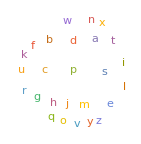

```mathematica
WordCloud[StringTake[WordList[ ],1]]
```

字符串不一定要包含文本。我们可以将罗马数字生成为字符串。

生成 1988 的罗马数字字符串：

```mathematica
RomanNumeral[1988]
```

MCMLXXXVIII

创建 20 以内的罗马数字列表：

```mathematica
Table[RomanNumeral[n],{n,20}]
```

{I,II,III,IV,V,VI,VII,VIII,IX,X,XI,XII,XIII,XIV,XV,XVI,XVII,XVIII,XIX,XX}

如同其它所有对象，我们也可以对这些字符串进行运算。例如，我们可以绘制连续的罗马数字的长度。

绘制 100 以内的罗马数字的长度：

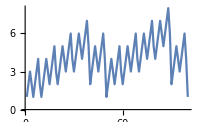

```mathematica
ListLinePlot[Table[StringLength[RomanNumeral[n]],{n,100}]]
```

IntegerName 将给出一个整数的英文名称。

给出整数 56 的名称：

```mathematica
IntegerName[56]
```

fifty-six

这里是英文整数名称的长度的线条图：

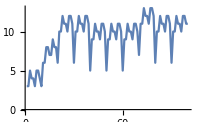

```mathematica
ListLinePlot[Table[StringLength[IntegerName[n]],{n,100}]]
```

有许多方法可以将字母变成数字(反之亦然)。

Alphabet 将给出字母列表：

```mathematica
Alphabet[ ]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

LetterNumber 将告诉你某个字母在字母表中出现的位置：

```mathematica
LetterNumber[{"a","b","x","y","z"}]
```

{1,2,24,25,26}

FromLetterNumber 则完成刚好相反的功能：

```mathematica
FromLetterNumber[{10,11,12,13,14,15}]
```

{j,k,l,m,n,o}

Alphabet 也知道非英语语言的字母表：

```mathematica
Alphabet["Russian"]
```

{а,б,в,г,д,е,ё,ж,з,и,й,к,л,м,н,о,п,р,с,т,у,ф,х,ц,ч,ш,щ,ъ,ы,ь,э,ю,я}

Transliterate 可以将其转换为(大致)相等的英文字母：

```mathematica
Transliterate[Alphabet["Russian"]]
```

{a,b,v,g,d,e,e,z,z,i,j,k,l,m,n,o,p,r,s,t,u,f,h,c,c,s,s,ʺ,y,ʹ,e,u,a}

将“wolfram”一词逐字转换为俄语字母：

```mathematica
Transliterate["wolfram","Russian"]
```

уолфрам

如果你需要，你也可以把文本变成图像，然后就可以使用图像处理。函数 Rasterize 可以创建一个光栅图像，或者位图。

生成一串文本的图像：

```mathematica
Rasterize[Style["ABC",100]]
```

-Graphics-

对它进行图像处理：

```mathematica
EdgeDetect[Rasterize[Style["ABC",100]]]
```

-Graphics-

词汇

"string" |   | 一个字符串
StringLength["string"] |   | 字符串的长度
StringReverse["string"] |   | 反转字符串
StringTake["string",4] |   | 从字符串起始位置取出字符
StringJoin["string","string"] |   | 将字符串连接在一起
StringJoin[{"string","string"}] |   | 连接一系列字符串
ToUpperCase["string"] |   | 将字符转换为大写形式
Characters["string"] |   | 将一个字符串转换为字符列表
TextWords["string"] |   | 从字符串中获取单词列表
TextSentences["string"] |   | 句子列表
WikipediaData["topic"] |   | 关于一个主题的维基百科文章
WordCloud["text"] |   | 基于词频的词云
WordList[ ] |   | 英语中常见单词的列表
Alphabet[ ] |   | 字母表中的字母列表
LetterNumber["c"] |   | 字母表中字母出现的位置
FromLetterNumber[n] |   | 字母表中某个位置的字母
Transliterate["text"] |   | 将任何语言的文本逐字转换成英语
Transliterate["text","alphabet"] |   | 将文本逐字转换为其它语言的字母
RomanNumeral[n] |   | 将一个数字转换为其罗马数字字符串
IntegerName[n] |   | 将一个数字转换为其英文名称字符串
InputForm["string"] |   | 显示一个带引号的字符串
Rasterize["string"] |   | 创建位图图像

"共有 30 道习题"
"以及 13 道附加题" | "开始练习 »"

将两个字符串 "Hello" 的副本连接起来。»

| 期望输出： |  
  | "HelloHello" |

将整个字母表以大写字母形式组成一个字符串。»

| 期望输出： |  
  | "ABCDEFGHIJKLMNOPQRSTUVWXYZ" |

将字母表以倒序形式组成一个字符串。»

| 期望输出： |  
  | "zyxwvutsrqponmlkjihgfedcba" |

将 100 个字符串 "AGCT" 的副本连接在一起。»

| 期望输出： |  
  | "AGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCT" |

使用 StringTake、StringJoin 以及 Alphabet 来得到 "abcdef"。»

| 期望输出： |  
  | "abcdef" |

使用字符串 "this is about strings" 来创建一个字母数量递增的列。»

| 期望输出： |  
  | "t"
"th"
"thi"
"this"
"this "
"this i"
"this is"
"this is "
"this is a"
"this is ab"
"this is abo"
"this is abou"
"this is about"
"this is about "
"this is about s"
"this is about st"
"this is about str"
"this is about stri"
"this is about strin"
"this is about string"
"this is about strings" |

将 “A long time ago, in a galaxy far, far away” 中每个单词的长度创建成条形图。»

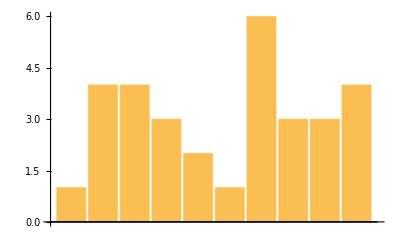
| 期望输出： |  
  | -Graphics- |

计算维基百科上关于 “computer” 的文章的字符串长度。»

| 期望输出示例： |  
  | 49848 |

计算维基百科上关于 “computer” 的文章有多少个词。»

| 期望输出示例： |  
  | 7742 |

找出维基百科上关于 “strings” 的文章的第一句话。»

| 期望输出示例： |  
  | "String is a flexible piece of rope or twine which is used to tie, bind, or hang other objects." |

用维基百科上关于 “computers” 的文章中所有句子的第一个字母组成一个字符串。»

| 期望输出示例： |  
  | "ASCTPMIDOMCPH="ITFTLTTTSITIIDMTTAAATTTIAATAIBIATITIITS=CATFTTTAEBNH=HTTTLHTWAB=THHHVTE=TDETTITPIRT=TEIBTDTTHACIINCTAILOIIIHBTCWATIHJTIWIAATBAITFCSTATHT=TDTKINHPTWTTTMIALITHTFMPWSTCBOTI=TTSTTITMWITCUTTS=FTHHIT=TEALTP=TBOBSA=TIET=CATDIRTPIWJSAITETSHTALATSGETTLSIETWOAMTTRACRIIISFIIGDOHCIAMTOBItSTBSITMSTSS=TITTITCIIA"QCSLTTT=W"A=HFMMH=C=C=W=T=TTSOSCT=" |

使用 WordList[ ] 找出英语单词中的最大单词长度。»

| 期望输出示例： |  
  | 23 |

计算 WordList[ ] 中以 “q” 开头的单词的数量。»

| 期望输出示例： |  
  | 197 |

将 WordList[ ] 中的前 1000 个单词的长度创建为线条图。»

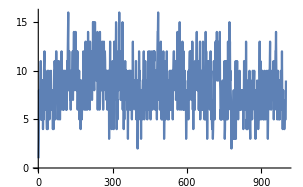
| 期望输出示例： |  
  | -Graphics- |

使用 StringJoin 和 Characters 将 WordList[ ] 中的所有字母组成一个词云。»

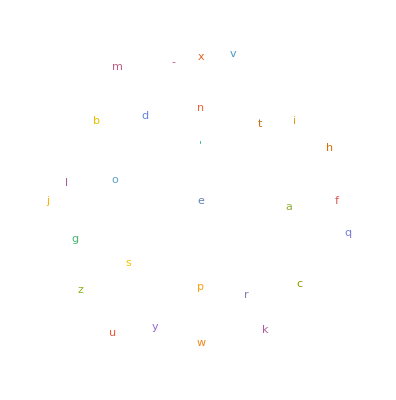
| 期望输出示例： |  
  | -Graphics- |

使用 StringReverse 将 WordList[ ] 中单词的最后一个字母组成一个词云。»

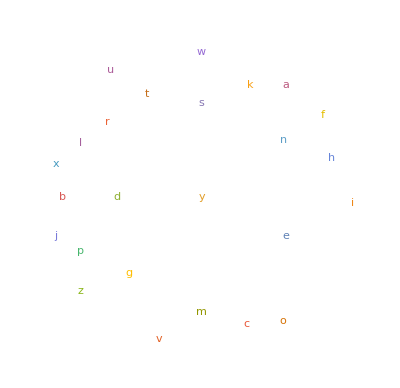
| 期望输出示例： |  
  | -Graphics- |

计算 1959 的罗马数字。»

| 期望输出： |  
  | "MCMLIX" |

计算从 1 到 2020 的罗马数字中的最大字符串长度。»

| 期望输出： |  
  | 13 |

将 100 以内的罗马数字的第一个字符组成一个词云。»

| 期望输出： |  
  |  |

使用 Length 来计算俄语字母表的长度。»

| 期望输出： |  
  | 33 |

生成大写的希腊字母表。»

| 期望输出： |  
  | {"Α","Β","Γ","Δ","Ε","Ζ","Η","Θ","Ι","Κ","Λ","Μ","Ν","Ξ","Ο","Π","Ρ","Σ","Τ","Υ","Φ","Χ","Ψ","Ω"} |

将 “wolfram” 中的字母编号创建为条形图。»

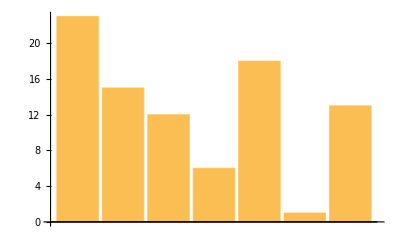
| 期望输出： |  
  | -Graphics- |

使用 FromLetterNumber 来创建一个由 1000 个随机字母组成的字符串。»

| 期望输出示例： |  
  | "chfpmqpcyncvrvvsczeyfihbbtyvwtejczkwdpfxwtfncqphiptelkyrkectbxxccksjxzubmcfsdveiexjzvldmyduewyayvstpajkttgelnayfsnlrnvmvhoomknurnjobsexzxiajjwdewgxldwjnwgqtmuwqalzopswwbvbrcdkaczpvpekkbcwotsevhukcbzjrbgtheypludcajvdcukftzsctsctvuimujiyrbgkaeuuiavggepzipouyhyvqlyjvbewluhqfgvmwwqtzjwmeoyjsbinlvmzpbjrdlelyrfzpwfjfhlowquqawzrbufvilscljlptgilvzggomjtlbtbvttwcqrucmsydwmbxqedqewjdfsevrzybymhwalzbaqazkhsrbfsalmtkxbcyxliaapasvdqvtqptoudinbabftutdoijvlmlgnodeiyprjkmfsdhdqmagbohksoyevwpljdmdglibgtrfbplfsewhrnoqnkryhaazlfqlikxmrwamtfdwiqyalivbqgrocsiavczjgtidffntqavtjtpwyjpbynwmmxfhnkzynrcvmewbtdsoanygujfooupnozbaetulhrpbngnxojqnbtsmtfelnrqsydvlxlxtcgfltegagyobeonakngwjchqgpycjdzaotfvxigouzmogrdpwwkkttsieddsmahqthvymvkcjlzigwenxvekurkixqjrormukhqyyzygvzntzptuooboriyjkaxofuediewvxrrifcdjfrlqeuneyrwppapdpooitwcevydjozxxfwlnzwulzjacoiryqogroikztsbbwbkfcjqvjlvdwabuiwoehnqbuxodlwnqidwbtzpbkdfwmjgtczbqbgldivjjprzuslsoszcghcklobxeknddhkgjvvhtsuffdrfhefjhawtxylpfxzjumgbcdhetsankemseloadcegkizwddlsqwzuxbpz" |

创建由 100 个包含 5 个随机字母的字符串组成的列表。»

| 期望输出示例： |  
  | {"vjdxl","yeftc","tguag","rsdyz","jvbgm","pdntg","wqupa","xznnh","gmuvl","nzxqd","qnokn","tyues","ukblh","mdats","pbjuu","hjifa","xnbtw","xquds","egttt","fkkax","udcrc","aucim","lulzv","isjpn","umgax","kdhoy","nysyq","ukhwl","remdz","ljjzn","ujtti","bircn","hnaqd","jhfwg","jlyju","jcegb","gcnso","rryks","hbnhg","gvoko","pcwjk","lnhps","umjom","knfia","gpxvw","esvzo","euiam","vxlnl","yajli","twfiz","veong","htndw","fggfy","jkvou","yurvh","buesn","svgzn","paevj","bmrza","hbiqc","cjazs","kkiuw","wtzrl","lqcpm","pwnng","xepji","wmmcl","fhlfe","thakf","nckgv","fzttu","hdffz","uadni","asfav","wouah","rtzaz","kjfhi","jaaiu","uinzk","bcarm","zujeq","icoko","ccaxw","eynlq","gnlso","jpkiu","wsrhb","bjlvz","ahdmc","nqpot","netkc","cxnzv","lyfky","uebwg","lklqj","iwvlp","ayxfv","rxjge","mheur","gxzmo"} |

将 “wolfram” 音译为希腊语。»

| 期望输出： |  
  | "βολφραμ" |

获取阿拉伯字母并将其逐字转换成英文。»

| 期望输出： |  
  | {"a","b","t","th","j","h","kh","d","dh","r","z","s","sh","s","d","t","z","ʿ","gh","f","q","k","l","m","n","h","w","y"} |

创建一个黑底白字字体大小为 200 的字母 “A”。»

| 期望输出： |  
  | -Graphics- |

使用 Manipulate 创建一个交互式选择器，由滑块来控制从字母表中选择一个字符，字符的字体大小为 100。»

| 期望输出： |  
  |  |

使用 Manipulate 来创建一个交互式选择器，从菜单中选择字母表中的一个字符，字符设置为字体大小为 100 的白底黑字轮廓的光栅图像。»

| 期望输出： |  
  |  |

使用 Manipulate 来创建一个“视觉模拟器”，使一个大小为 200 的字母 “A” 在 0 到 50 的范围内模糊。»

| 期望输出： |  
  |  |

生成一个由字母表和倒序字母表组成的字符串。»

| 期望输出： |  
  | "abcdefghijklmnopqrstuvwxyzzyxwvutsrqponmlkjihgfedcba" |

将字母表及其倒序创建为一列。»

| 期望输出： |  
  | "abcdefghijklmnopqrstuvwxyz"
"zyxwvutsrqponmlkjihgfedcba" |

计算维基百科上关于 “computer” 的文章中有多少句话。»

| 期望输出： |  
  | 339 |

将维基百科上关于 “strings” 的文章的第一句话中的单词连在一起，不要有空格。»

| 期望输出： |  
  | "Stringisaflexiblepieceofropeortwinewhichisusedtotiebindorhangotherobjects" |

找出维基百科上关于 “computers” 的文章中最长的一个单词的长度。»

| 期望输出： |  
  | 20 |

绘制出 2000 以内的罗马数字的长度的线条图。»

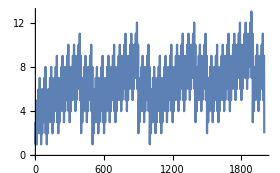
| 期望输出： |  
  | -Graphics- |

将 100 以内的罗马数字连接成一个字符串。»

| 期望输出： |  
  | "IIIIIIIVVVIVIIVIIIIXXXIXIIXIIIXIVXVXVIXVIIXVIIIXIXXXXXIXXIIXXIIIXXIVXXVXXVIXXVIIXXVIIIXXIXXXXXXXIXXXIIXXXIIIXXXIVXXXVXXXVIXXXVIIXXXVIIIXXXIXXLXLIXLIIXLIIIXLIVXLVXLVIXLVIIXLVIIIXLIXLLILIILIIILIVLVLVILVIILVIIILIXLXLXILXIILXIIILXIVLXVLXVILXVIILXVIIILXIXLXXLXXILXXIILXXIIILXXIVLXXVLXXVILXXVIILXXVIIILXXIXLXXXLXXXILXXXIILXXXIIILXXXIVLXXXVLXXXVILXXXVIILXXXVIIILXXXIXXCXCIXCIIXCIIIXCIVXCVXCVIXCVIIXCVIIIXCIXC" |

将 30 以内的所有罗马数字连接在一起，然后绘制字母编号的线条图。»

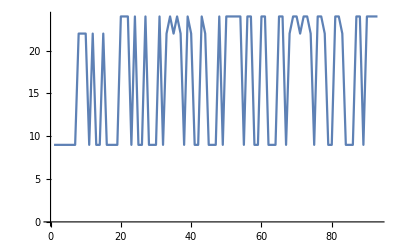
| 期望输出： |  
  | -Graphics- |

找到 1000 以内整数的名称的最大字符串长度。»

| 期望输出： |  
  | 27 |

创建由使用随机颜色显示，字体大小为 20 的大写字母组成的列表。»

| 期望输出： |  
  | {"A","B","C","D","E","F","G","H","I","J","K","L","M","N","O","P","Q","R","S","T","U","V","W","X","Y","Z"} |

创建由 100 个包含 5 个随机俄语字母的字符串组成的列表。»

| 期望输出： |  
  | {"щёярф","цруйл","пхёкц","вгхфв","флэшм","яёуйу","лчтло","гнхшу","клчщч","эйарэ","совэф","цхшни","кдпфз","здъжь","ыйряп","змгщд","яфтбм","каоеэ","лкжрб","уатоо","нзквк","сонль","юфщзс","ябгшш","нясзо","хоэсв","псикх","днэхх","ъбшнщ","вюадг","ъчизб","цпвюа","ныиья","пгбби","ыхжзй","хвзет","чивир","чзгвм","млчюн","шгшнж","снслж","жйзьа","вйрак","вжънх","иёжщи","кшъиф","йцюую","цизшз","юшеях","хещэб","ффвмв","юяяко","лчвля","фцаьс","чрхиь","пунзщ","резуя","мпущд","гызшг","кёжмэ","бзяёя","хдхдъ","юзфща","ызуцр","ьяящл","оэмщи","эгщов","уфпвл","ядьщэ","йуэёэ","цснск","йпцжъ","йгухл","урмщр","щгхоф","ащвфх","кчьаь","улчпу","асмлж","какхй","рврвг","олйзя","ёцшцэ","энсав","еёяуб","чцеяс","вшэеи","чомры","ипбьэ","ьяфым","шидяб","щаюкы","шобро","айэнй","ашфгк","съгрм","ыфафщ","пбянс","фмсгф","хрубё"} |

创建一个操作界面来显示字体大小为 200 的字母 A 的边缘，模糊程度 从 0 变化到 50。»

| 期望输出： |  
  |  |

将黑底白字字体大小为 200 的字母 A 和 B 相加在一起。»

| 期望输出： |  
  | -Graphics- |

问&答

"x" 和 x 之间的区别是什么？

"x" 是一个字符串，而 x 是一个 Wolfram 语言符号，就像 Plus 或者 Max 一样，可以被定义为进行实际的计算。我们在后面会更多地谈论符号。

我怎样才能输入键盘上没有的字符？

你可以使用你的计算机提供的任何方法，或者你也可以直接使用 Wolfram 语言提供的构造方法，比如  \[Alpha]。

如何将引号(")放在一个字符串内？

使用 \"(如果你想把 \" 按原始形式放在字符串中，就要使用\\\")。(如果你想把 \\\" 放进去，就需要用到很多反斜线 \\\\\\\"。)

词云中元素的颜色是如何确定的？

默认情况下，它是使用某个调色板内的随机颜色。如果你需要，也可以进行指定。

为什么词云中显示“s”是最常见的字母？

因为它是英语中常见单词里面最常见的第一个字母。如果你查看的是所有字母，最常见的是“e”。

那些不是英语的字母呢？它们是如何编号的？
What about letters that aren’t English? How are they numbered?

LetterNumber["α","Greek"] 将给出希腊字母表的编号。所有的字符都被分配了一个字符代码。你可以用 ToCharacterCode 来找到它。

Wolfram 语言知道哪些字母？

基本上囊括当今在使用的所有字母。试试“Greek”或者“Arabic”，或者一种语言的名称。请注意，当某种语言使用重音字符时，有时很难确定哪些是“在”字母表中，哪些是由字母表衍生出来的。

我可以翻译单词而不只是翻译字母吗？

是的，使用 WordTranslation。详见第 35 节。

我可以得到英语以外的其他语言的常用单词表吗？

是的，请使用 WordList[Language→"Spanish"] 等等。

技术笔记

RandomWord[10] 将给出 10 个随机单词，你认识其中多少个？

StringTake["string",-2] 将从字符串的末尾取出两个字符。

每一个字符，无论是“a”、“α”或者“狼”，都由一个 Unicode 字符码表示，用 ToCharacterCode 可以找到。你可以用 FromCharacterCode 来探索“Unicode 空间”。

如果你从 WikipediaData 得到了不同的结果，那是因为维基百科页面已经被更改。

WordCloud 会自动删除文本中的“无趣”词汇，比如如“the”、“and”等等。

如果你搞不清楚某个字母或语言的名称，可以使用ctrl=(将在第 16 节进行讨论)，来以自然语言的形式给出它。

探索更多

Wolfram 语言中的字符串操作指南 »